# Nuclear Scattering

## Potential

```mathematica
(* Woods-Saxon *)
WS=Compile[{{r,_Real},{r0,_Real},{a,_Real},{V0,_Real}},-V0/(1+Exp[(r-r0)/a]),Parallelization->True];
(* Columb potential *)
Coul=Compile[{{r,_Real},{Rc,_Real},{Z1,_Integer},{Z2,_Integer}},With[{e=1},If[r≥ Rc,Z1 Z2 e^2/r,Z1 Z2 e^2/(2Rc)(3-(r/Rc)^2)]],Parallelization->True];
```

```mathematica
Manipulate[
Plot[
{WS[r,r0,a,V0],Coul[r,Rc,1,1],WS[r,r0,a,V0]+Coul[r,Rc,1,1]}
,{r,0,10},PlotRange->20, PlotStyle->{Red,Green, Blue}]
,{{r0,4},1,9},{{a,0.4},0.1,1},{V0,10, 50},{Rc,0,5}]
```

## Schrodinger equation

### Numerov' s method

```mathematica
The Radial part is
D[x[r],{r,2}]+2/r D[x[r],r]-(l(l+1))/r^2 x[r]+k^2 x[r]==0
```

```mathematica
D[x[r]/r,{r,2}]+2/r D[x[r]/r,r]-(l(l+1))/r^2 x[r]/r+k^2 x[r]/r==0//FullSimplify
```

r x''[r]==((l+l^2-k^2 r^2) x[r])/r

```mathematica
r^2 D[x[r],{r,2}]-l(l+1)x[r]+r^2 V[r]x[r]+k^2 r^2 x[r]==0
```

```mathematica
Veff[x_,energy_,l_]:=(energy-0)-(l(l+1))/x^2;
```

```mathematica
Remove[WaveR]
```

```mathematica
WaveR[energy_,l_,step_,Δstep_]:=Module[{G},
G=Array[y,step+1,0];
y[0]==0;
y[1]==1;
Table[y[n+1]== ((2-5/6 Δstep^2 Veff[n Δstep,energy,l])y[n]-(1+1/12 Δstep^2 Veff[(n-1) Δstep,energy,l])y[n-1])/(1+Δstep^2/12 Veff[(n+1) Δstep,energy,l]),{n,1,step}]
];
```

```mathematica
WaveR[1,0,50,0.2]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{y[2]==Indeterminate,y[3]==0.996678 (-1.00333 y[1]+1.96667 y[2]),y[4]==0.996678 (-1.00333 y[2]+1.96667 y[3]),y[5]==0.996678 (-1.00333 y[3]+1.96667 y[4]),y[6]==0.996678 (-1.00333 y[4]+1.96667 y[5]),y[7]==0.996678 (-1.00333 y[5]+1.96667 y[6]),y[8]==0.996678 (-1.00333 y[6]+1.96667 y[7]),y[9]==0.996678 (-1.00333 y[7]+1.96667 y[8]),y[10]==0.996678 (-1.00333 y[8]+1.96667 y[9]),y[11]==0.996678 (-1.00333 y[9]+1.96667 y[10]),y[12]==0.996678 (-1.00333 y[10]+1.96667 y[11]),y[13]==0.996678 (-1.00333 y[11]+1.96667 y[12]),y[14]==0.996678 (-1.00333 y[12]+1.96667 y[13]),y[15]==0.996678 (-1.00333 y[13]+1.96667 y[14]),y[16]==0.996678 (-1.00333 y[14]+1.96667 y[15]),y[17]==0.996678 (-1.00333 y[15]+1.96667 y[16]),y[18]==0.996678 (-1.00333 y[16]+1.96667 y[17]),y[19]==0.996678 (-1.00333 y[17]+1.96667 y[18]),y[20]==0.996678 (-1.00333 y[18]+1.96667 y[19]),y[21]==0.996678 (-1.00333 y[19]+1.96667 y[20]),y[22]==0.996678 (-1.00333 y[20]+1.96667 y[21]),y[23]==0.996678 (-1.00333 y[21]+1.96667 y[22]),y[24]==0.996678 (-1.00333 y[22]+1.96667 y[23]),y[25]==0.996678 (-1.00333 y[23]+1.96667 y[24]),y[26]==0.996678 (-1.00333 y[24]+1.96667 y[25]),y[27]==0.996678 (-1.00333 y[25]+1.96667 y[26]),y[28]==0.996678 (-1.00333 y[26]+1.96667 y[27]),y[29]==0.996678 (-1.00333 y[27]+1.96667 y[28]),y[30]==0.996678 (-1.00333 y[28]+1.96667 y[29]),y[31]==0.996678 (-1.00333 y[29]+1.96667 y[30]),y[32]==0.996678 (-1.00333 y[30]+1.96667 y[31]),y[33]==0.996678 (-1.00333 y[31]+1.96667 y[32]),y[34]==0.996678 (-1.00333 y[32]+1.96667 y[33]),y[35]==0.996678 (-1.00333 y[33]+1.96667 y[34]),y[36]==0.996678 (-1.00333 y[34]+1.96667 y[35]),y[37]==0.996678 (-1.00333 y[35]+1.96667 y[36]),y[38]==0.996678 (-1.00333 y[36]+1.96667 y[37]),y[39]==0.996678 (-1.00333 y[37]+1.96667 y[38]),y[40]==0.996678 (-1.00333 y[38]+1.96667 y[39]),y[41]==0.996678 (-1.00333 y[39]+1.96667 y[40]),y[42]==0.996678 (-1.00333 y[40]+1.96667 y[41]),y[43]==0.996678 (-1.00333 y[41]+1.96667 y[42]),y[44]==0.996678 (-1.00333 y[42]+1.96667 y[43]),y[45]==0.996678 (-1.00333 y[43]+1.96667 y[44]),y[46]==0.996678 (-1.00333 y[44]+1.96667 y[45]),y[47]==0.996678 (-1.00333 y[45]+1.96667 y[46]),y[48]==0.996678 (-1.00333 y[46]+1.96667 y[47]),y[49]==0.996678 (-1.00333 y[47]+1.96667 y[48]),y[50]==0.996678 (-1.00333 y[48]+1.96667 y[49]),y[51]==0.996678 (-1.00333 y[49]+1.96667 y[50])}

### Nuclear Force

H Ψ= (- ℏ^2)/(2m)Laplacian[Ψ]+V_n Ψ = Eenergy Ψ
 Ψ=Φ+Ψscat
Ψ=∑ u[r]Y[l,m]^*Y[l,m]
-ℏ^2/(2m)(u''[r]+2/r u'[r]-(l(l+1))/r^2 u[r])+V[r] u[r]==Energy u[r]
This represent the r→∞

```mathematica
DSolve[-ℏ^2/(2m)(u''[r]+2/r u'[r]-(l(l+1))/r^2 u[r])==Energy u[r],u[r],r]
```

{{u[r]→C[1] SphericalBesselJ[l,(√2 √Energy √m r)/ℏ]+C[2] SphericalBesselY[l,(√2 √Energy √m r)/ℏ]}}

```mathematica
Manipulate[Plot[{SphericalBesselJ[l,x],SphericalBesselY[l,x],1/x Sin[x-l/2 π]},{x,20,30}],{l,Table[i,{i,0,3,1}]}]
```

The asympotic behaviour
Ψ[r] = A( Exp[ⅈ k r] + f[θ] Exp[ⅈ k r]/r)
the solution 
Ψ[r] = Sum[c[l] (SphericalBeseelJ[l, k r] -Tan[δ] SphericalBesselY[l,k r]) LegendreP[l, Cos[θ]], for m = 0 as no preference in space or isotropic.
then,

```mathematica
f[θ_,k_,lmax_,δ_]:=1/(ⅈ 2 k)Sum[(2l+1)(Exp[2 ⅈ Composition[δ][l,k]]-1)LegendreP[l,Cos[θ]],{l,0,lmax}]
```

```mathematica
f[θ,k,0,δ]
```

-(ⅈ (-1+ⅇ^(2 ⅈ ArcTan[-SphericalBesselY[0,k],-SphericalBesselJ[0,k]])))/(2 k)

### Nuclear Force + Coulomb Force (not finsih)

For charger system, the Coulomb Force is needed. the modified Schrodinger equation is:
(d^2/dr^2-(l(l+1))/r^2-2η k/r+k^2)R_l=0
where 
η = (Z_1 Z_2 e^2)/(ℏ ν)

```mathematica
DSolve[u''[r]-(l(l+1))/r^2 u[r]-2(η k)/r u[r]+k^2 u[r]==0,u[r],r]//Simplify
```

{{u[r]→C[1] WhittakerM[ⅈ η,1/2+l,2 ⅈ k r]+C[2] WhittakerW[ⅈ η,1/2+l,2 ⅈ k r]}}

```mathematica
FunctionExpand[WhittakerM[ⅈ η,1/2 (1+2 l),2 ⅈ k r]]//Simplify
FunctionExpand[WhittakerW[ⅈ η,1/2+l,2 ⅈ k r]]//Simplify
```

2^(1+l) ⅇ^(-ⅈ k r) (ⅈ k r)^(1+l) Hypergeometric1F1[1+l-ⅈ η,2+2 l,2 ⅈ k r]

2^-l ⅇ^(-ⅈ k r) (ⅈ k r)^-l HypergeometricU[-l-ⅈ η,-2 l,2 ⅈ k r]

```mathematica
Manipulate[
Plot[{
ⅇ^(-ⅈ x)Hypergeometric1F1[1+l-ⅈ η,2 (1+l),2 ⅈ x],
Re[ⅇ^(-ⅈ x) HypergeometricU[-l-ⅈ η,-2 l,2 ⅈ x]]
},{x,0,30},PlotRange->{-4,12}],{l,Table[i,{i,0,3,1}]},{{η,0},0,10}]
```

```mathematica
DSolve[u''[r]+2/r u'[r]-(l(l+1))/r^2 u[r]-2 η/r u[r]+k^2 u[r]==0,u[r],r]//Simplify
```

{{u[r]→ⅇ^(-ⅈ k r) r^l (C[1] HypergeometricU[1+l-(ⅈ η)/k,2 (1+l),2 ⅈ k r]+C[2] LaguerreL[-1-l+(ⅈ η)/k,1+2 l,2 ⅈ k r])}}

```mathematica
Manipulate[Plot[{Im[WhittakerM[ⅈ η,1/2 +l,2 ⅈ  x]],Re[WhittakerW[ⅈ η,1/2 + l,2 ⅈ x]]},{x,0,30},PlotRange->{-4,12}],{l,Table[i,{i,0,3,1}]},{{η,0},0,10}]
```

### Rutherford Cross section

```mathematica
fc[θ_,η_,k_,σ0_]:=-η/(2k Sin[θ/2]^2)Exp[2ⅈ(σ0-η Log[Sin[θ/2]]) ]
```

```mathematica
dscRF[θ_,energy_,Z1_,Z2_]:=With[{e=1},((Z1 Z2 e^2)/(4 energy (Sin[θ/2])^2))^2]
```

```mathematica
Manipulate[Plot[dscRF[θ,energy,1,1],{θ,0,π},PlotRange->{0,20}],{energy,1,100}]
```

### Cross section

```mathematica
g[l_,k_]:=0
Ndsc[θ_,η_,k_,σ0_,lmax_,α_]:=Abs[fc[θ,η,k,σ0]+α f[θ,k,lmax,δ]]^2/Abs[fc[θ,η,k,σ0]]^2
Manipulate[Plot[Ndsc[θ,η,k,0,4,α],{θ,0,π},PlotRange->{0,1.1}],{η,1,2},{k,1,20},{α,0,1}]
```

### General (Numerical Solution)

```mathematica
Remove[p]
```

```mathematica
h[l_,k_,p_]:=NDSolve[{p''[r]+2/r p'[r]-(l(l+1))/r^2 p[r]+k^2 p[r]+WS[r,2,0.1,10]p[r]+Coul[r,0,1,1]p[r]==0,p[0.01]==0, p'[0.01]==0.1},p[r],{r,0.01,30}]
```

CompiledFunction::cfsa: Argument r at position 1 should be a "machine-size real number".

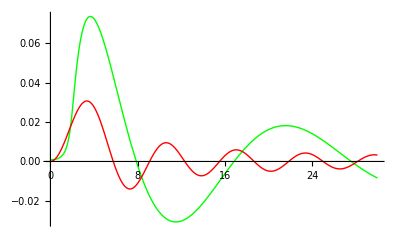

```mathematica
Show[
Plot[Evaluate[p[r]/.h[0,0.2,p]],{r,0.01,30},PlotStyle->Green],
Plot[SphericalBesselJ[2,r]/10,{r,0.01,30},PlotStyle->Red](*,
Plot[SphericalBesselY[2,r]2000,{r,0.01,30},PlotStyle->Blue]*)
]
```

## Phase Shift

### Hard Sphere

Boundary condition:
continous at r=a, Ψ[a]==0

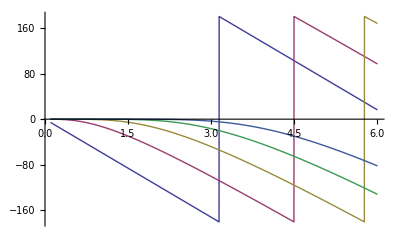

```mathematica
δ[l_,ka_]:=ArcTan[-SphericalBesselY[l,ka],-SphericalBesselJ[l,ka]]
Plot[Evaluate[Table[(δ[l,x])180/π,{l,0,4}]],{x,0.1,6}]
```

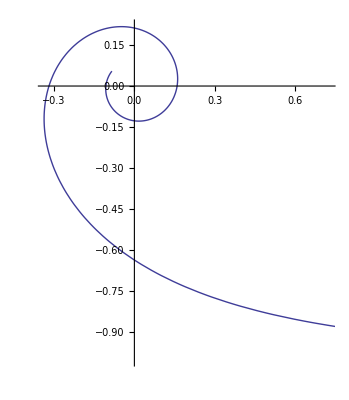

```mathematica
ParametricPlot[{-SphericalBesselY[0,ka],-SphericalBesselJ[0,ka]},{ka,0,10}]
```

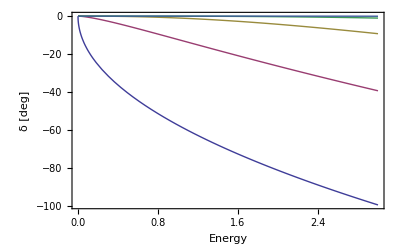

```mathematica
Plot[Evaluate[Table[δ[l,√energy],{l,0,4}]],{energy,0,3},Frame->True, FrameLabel->{"Energy","δ [deg]"}]
```